```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab4

```mathematica
constF4u = Import["constF4_u.txt","Table"][[1]]
constF4c = Import["constF4_c.txt","Table"][[1]]
constF128u = Import["constF128_u.txt","Table"][[1]]
constF128c = Import["constF128_c.txt","Table"][[1]]
```

{1.11022×10^-16,3.33067×10^-16,3.05311×10^-16,8.32667×10^-17,1}

{3.33067×10^-16,4.60391×10^-16,-8.66903×10^-16,-1.395×10^-16,1}

{-4.48598×10^37,6.68357×10^36,9.90185×10^38,-1.42697×10^38,-1.06465×10^40,1.45523×10^39,7.43319×10^40,-9.3762×10^39,-3.79154×10^41,4.17415×10^40,1.5059×10^42,-1.30856×10^41,-4.84205×10^42,2.72116×10^41,1.29283×10^43,-2.46028×10^41,-2.91619×10^43,-6.51091×10^41,5.62597×10^43,3.63906×10^42,-9.37461×10^43,-9.81815×10^42,1.3618×10^44,1.91017×10^43,-1.74017×10^44,-2.97589×10^43,1.97304×10^44,3.89645×10^43,-1.99961×10^44,-4.44636×10^43,1.82075×10^44,4.54729×10^43,-1.49616×10^44,-4.16551×10^43,1.10456×10^44,3.6185×10^43,-7.35414×10^43,-2.8688×10^43,4.08949×10^43,1.91461×10^43,-1.94603×10^43,-9.45783×10^42,9.7077×10^42,5.26154×10^42,-2.88617×10^42,-1.1511×10^42,2.2997×10^42,9.66666×10^41,-1.04472×10^41,7.26577×10^41,2.19695×10^42,1.77204×10^42,5.20261×10^41,-7.02179×10^41,-7.73994×10^41,-1.52056×10^40,1.1024×10^42,1.99084×10^42,2.54183×10^42,2.84032×10^42,3.03586×10^42,3.19459×10^42,3.31473×10^42,3.35973×10^42,3.29706×10^42,3.11595×10^42,2.82899×10^42,2.46476×10^42,2.05853×10^42,1.64469×10^42,1.2521×10^42,9.01904×10^41,6.07095×10^41,3.73057×10^41,1.98628×10^41,7.76984×10^40,1.14419×10^39,-4.12759×10^40,-5.9427×10^40,-6.1866×10^40,-5.54029×10^40,-4.50095×10^40,-3.39537×10^40,-2.40811×10^40,-1.61781×10^40,-1.03442×10^40,-6.31219×10^39,-3.67987×10^39,-2.04821×10^39,-1.08599×10^39,-5.46469×10^38,-2.59629×10^38,-1.15701×10^38,-4.79556×10^37,-1.82681×10^37,-6.27266×10^36,-1.86582×10^36,-4.29847×10^35,-3.7899×10^34,3.53268×10^34,3.11905×10^34,1.75341×10^34,8.19633×10^33,3.38478×10^33,1.25041×10^33,4.08593×10^32,1.13658×10^32,2.40872×10^31,2.03791×10^30,-1.3928×10^30,-1.03858×10^30,-4.63565×10^29,-1.64846×10^29,-5.01182×10^28,-1.3383×10^28,-3.17573×10^27,-6.72906×10^26,-1.27431×10^26,-2.15298×10^25,-3.23232×10^24,-4.28506×10^23,-4.97067×10^22,-4.9809×10^21,-4.23365×10^20,-2.97271×10^19,-1.65686×10^18,-6.87199×10^16,-1.88345×10^15,-2.55324×10^13}

{-1.96412×10^22,9.01508×10^21,6.32643×10^23,-2.90122×10^23,-9.94454×10^24,4.52677×10^24,1.01759×10^26,-4.58367×10^25,-7.62496×10^26,3.39232×10^26,4.46293×10^27,-1.96408×10^27,-2.12382×10^28,9.27371×10^27,8.44087×10^28,-3.65731×10^28,-2.85673×10^29,1.21031×10^29,8.41842×10^29,-3.49655×10^29,-2.19465×10^30,9.51944×10^29,4.97063×10^30,-2.18226×10^30,-1.0396×10^31,5.97717×10^30,1.59662×10^31,-9.39573×10^30,-2.14445×10^31,1.35031×10^31,-1.75733×10^31,1.55563×10^32,-2.21806×10^32,-4.07661×10^32,2.02917×10^33,-3.41226×10^33,1.05178×10^33,9.07797×10^33,-2.6364×10^34,4.53289×10^34,-8.39179×10^34,2.57958×10^35,-8.58188×10^35,2.2388×10^36,-4.16961×10^36,4.47328×10^36,2.32692×10^36,-2.4599×10^37,7.05913×10^37,-1.44707×10^38,2.41293×10^38,-3.12302×10^38,1.53926×10^38,8.33102×10^38,-3.94727×10^39,1.13229×10^40,-2.56284×10^40,4.93146×10^40,-8.36283×10^40,1.26662×10^41,-1.66494×10^41,1.61732×10^41,-4.53086×10^39,-5.20889×10^41,1.74166×10^42,-4.00883×10^42,7.5228×10^42,-1.22076×10^43,1.78758×10^43,-2.47998×10^43,3.42904×10^43,-4.81507×10^43,6.55239×10^43,-7.64786×10^43,5.39524×10^43,5.14628×10^43,-3.07922×10^44,7.85808×10^44,-1.52981×10^45,2.5283×10^45,-3.69361×10^45,4.86549×10^45,-5.84222×10^45,6.43215×10^45,-6.5088×10^45,6.0493×10^45,-5.14169×10^45,3.95855×10^45,-2.70686×10^45,1.57301×10^45,-6.81407×10^44,7.8435×10^43,2.57913×10^44,-3.91725×10^44,3.99153×10^44,-3.45546×10^44,2.74658×10^44,-2.08769×10^44,1.55027×10^44,-1.1298×10^44,8.00854×10^43,-5.43182×10^43,3.46113×10^43,-2.03435×10^43,1.08104×10^43,-5.04884×10^42,1.96172×10^42,-5.3869×10^41,1.01643×10^40,1.1551×10^41,-1.0103×10^41,6.03046×10^40,-2.93328×10^40,1.22486×10^40,-4.48282×10^39,1.45045×10^39,-4.16003×10^38,1.05657×10^38,-2.36742×10^37,4.65088×10^36,-7.94045×10^35,1.16416×10^35,-1.4423×10^34,1.47717×10^33,-1.21246×10^32,7.61575×10^30,-3.3978×10^29,9.38259×10^27,-1.14912×10^26}

```mathematica
poly4u = ∑_(k=1)^(Length@constF4u) constF4u[[k]]*x^(Length@constF4u-k)
poly4c = ∑_(k=1)^(Length@constF4c) constF4c[[k]]*x^(Length@constF4c-k)
poly128u = ∑_(k=1)^(Length@constF128u) constF128u[[k]]*x^(Length@constF128u-k)
poly128c = ∑_(k=1)^(Length@constF128c) constF128c[[k]]*x^(Length@constF128c-k)
```

1+8.32667×10^-17 x+3.05311×10^-16 x^2+3.33067×10^-16 x^3+1.11022×10^-16 x^4

1-1.395×10^-16 x-8.66903×10^-16 x^2+4.60391×10^-16 x^3+3.33067×10^-16 x^4

-2.55324×10^13-1.88345×10^15 x-6.87199×10^16 x^2-1.65686×10^18 x^3-2.97271×10^19 x^4-4.23365×10^20 x^5-4.9809×10^21 x^6-4.97067×10^22 x^7-4.28506×10^23 x^8-3.23232×10^24 x^9-2.15298×10^25 x^10-1.27431×10^26 x^11-6.72906×10^26 x^12-3.17573×10^27 x^13-1.3383×10^28 x^14-5.01182×10^28 x^15-1.64846×10^29 x^16-4.63565×10^29 x^17-1.03858×10^30 x^18-1.3928×10^30 x^19+2.03791×10^30 x^20+2.40872×10^31 x^21+1.13658×10^32 x^22+4.08593×10^32 x^23+1.25041×10^33 x^24+3.38478×10^33 x^25+8.19633×10^33 x^26+1.75341×10^34 x^27+3.11905×10^34 x^28+3.53268×10^34 x^29-3.7899×10^34 x^30-4.29847×10^35 x^31-1.86582×10^36 x^32-6.27266×10^36 x^33-1.82681×10^37 x^34-4.79556×10^37 x^35-1.15701×10^38 x^36-2.59629×10^38 x^37-5.46469×10^38 x^38-1.08599×10^39 x^39-2.04821×10^39 x^40-3.67987×10^39 x^41-6.31219×10^39 x^42-1.03442×10^40 x^43-1.61781×10^40 x^44-2.40811×10^40 x^45-3.39537×10^40 x^46-4.50095×10^40 x^47-5.54029×10^40 x^48-6.1866×10^40 x^49-5.9427×10^40 x^50-4.12759×10^40 x^51+1.14419×10^39 x^52+7.76984×10^40 x^53+1.98628×10^41 x^54+3.73057×10^41 x^55+6.07095×10^41 x^56+9.01904×10^41 x^57+1.2521×10^42 x^58+1.64469×10^42 x^59+2.05853×10^42 x^60+2.46476×10^42 x^61+2.82899×10^42 x^62+3.11595×10^42 x^63+3.29706×10^42 x^64+3.35973×10^42 x^65+3.31473×10^42 x^66+3.19459×10^42 x^67+3.03586×10^42 x^68+2.84032×10^42 x^69+2.54183×10^42 x^70+1.99084×10^42 x^71+1.1024×10^42 x^72-1.52056×10^40 x^73-7.73994×10^41 x^74-7.02179×10^41 x^75+5.20261×10^41 x^76+1.77204×10^42 x^77+2.19695×10^42 x^78+7.26577×10^41 x^79-1.04472×10^41 x^80+9.66666×10^41 x^81+2.2997×10^42 x^82-1.1511×10^42 x^83-2.88617×10^42 x^84+5.26154×10^42 x^85+9.7077×10^42 x^86-9.45783×10^42 x^87-1.94603×10^43 x^88+1.91461×10^43 x^89+4.08949×10^43 x^90-2.8688×10^43 x^91-7.35414×10^43 x^92+3.6185×10^43 x^93+1.10456×10^44 x^94-4.16551×10^43 x^95-1.49616×10^44 x^96+4.54729×10^43 x^97+1.82075×10^44 x^98-4.44636×10^43 x^99-1.99961×10^44 x^100+3.89645×10^43 x^101+1.97304×10^44 x^102-2.97589×10^43 x^103-1.74017×10^44 x^104+1.91017×10^43 x^105+1.3618×10^44 x^106-9.81815×10^42 x^107-9.37461×10^43 x^108+3.63906×10^42 x^109+5.62597×10^43 x^110-6.51091×10^41 x^111-2.91619×10^43 x^112-2.46028×10^41 x^113+1.29283×10^43 x^114+2.72116×10^41 x^115-4.84205×10^42 x^116-1.30856×10^41 x^117+1.5059×10^42 x^118+4.17415×10^40 x^119-3.79154×10^41 x^120-9.3762×10^39 x^121+7.43319×10^40 x^122+1.45523×10^39 x^123-1.06465×10^40 x^124-1.42697×10^38 x^125+9.90185×10^38 x^126+6.68357×10^36 x^127-4.48598×10^37 x^128

-1.14912×10^26+9.38259×10^27 x-3.3978×10^29 x^2+7.61575×10^30 x^3-1.21246×10^32 x^4+1.47717×10^33 x^5-1.4423×10^34 x^6+1.16416×10^35 x^7-7.94045×10^35 x^8+4.65088×10^36 x^9-2.36742×10^37 x^10+1.05657×10^38 x^11-4.16003×10^38 x^12+1.45045×10^39 x^13-4.48282×10^39 x^14+1.22486×10^40 x^15-2.93328×10^40 x^16+6.03046×10^40 x^17-1.0103×10^41 x^18+1.1551×10^41 x^19+1.01643×10^40 x^20-5.3869×10^41 x^21+1.96172×10^42 x^22-5.04884×10^42 x^23+1.08104×10^43 x^24-2.03435×10^43 x^25+3.46113×10^43 x^26-5.43182×10^43 x^27+8.00854×10^43 x^28-1.1298×10^44 x^29+1.55027×10^44 x^30-2.08769×10^44 x^31+2.74658×10^44 x^32-3.45546×10^44 x^33+3.99153×10^44 x^34-3.91725×10^44 x^35+2.57913×10^44 x^36+7.8435×10^43 x^37-6.81407×10^44 x^38+1.57301×10^45 x^39-2.70686×10^45 x^40+3.95855×10^45 x^41-5.14169×10^45 x^42+6.0493×10^45 x^43-6.5088×10^45 x^44+6.43215×10^45 x^45-5.84222×10^45 x^46+4.86549×10^45 x^47-3.69361×10^45 x^48+2.5283×10^45 x^49-1.52981×10^45 x^50+7.85808×10^44 x^51-3.07922×10^44 x^52+5.14628×10^43 x^53+5.39524×10^43 x^54-7.64786×10^43 x^55+6.55239×10^43 x^56-4.81507×10^43 x^57+3.42904×10^43 x^58-2.47998×10^43 x^59+1.78758×10^43 x^60-1.22076×10^43 x^61+7.5228×10^42 x^62-4.00883×10^42 x^63+1.74166×10^42 x^64-5.20889×10^41 x^65-4.53086×10^39 x^66+1.61732×10^41 x^67-1.66494×10^41 x^68+1.26662×10^41 x^69-8.36283×10^40 x^70+4.93146×10^40 x^71-2.56284×10^40 x^72+1.13229×10^40 x^73-3.94727×10^39 x^74+8.33102×10^38 x^75+1.53926×10^38 x^76-3.12302×10^38 x^77+2.41293×10^38 x^78-1.44707×10^38 x^79+7.05913×10^37 x^80-2.4599×10^37 x^81+2.32692×10^36 x^82+4.47328×10^36 x^83-4.16961×10^36 x^84+2.2388×10^36 x^85-8.58188×10^35 x^86+2.57958×10^35 x^87-8.39179×10^34 x^88+4.53289×10^34 x^89-2.6364×10^34 x^90+9.07797×10^33 x^91+1.05178×10^33 x^92-3.41226×10^33 x^93+2.02917×10^33 x^94-4.07661×10^32 x^95-2.21806×10^32 x^96+1.55563×10^32 x^97-1.75733×10^31 x^98+1.35031×10^31 x^99-2.14445×10^31 x^100-9.39573×10^30 x^101+1.59662×10^31 x^102+5.97717×10^30 x^103-1.0396×10^31 x^104-2.18226×10^30 x^105+4.97063×10^30 x^106+9.51944×10^29 x^107-2.19465×10^30 x^108-3.49655×10^29 x^109+8.41842×10^29 x^110+1.21031×10^29 x^111-2.85673×10^29 x^112-3.65731×10^28 x^113+8.44087×10^28 x^114+9.27371×10^27 x^115-2.12382×10^28 x^116-1.96408×10^27 x^117+4.46293×10^27 x^118+3.39232×10^26 x^119-7.62496×10^26 x^120-4.58367×10^25 x^121+1.01759×10^26 x^122+4.52677×10^24 x^123-9.94454×10^24 x^124-2.90122×10^23 x^125+6.32643×10^23 x^126+9.01508×10^21 x^127-1.96412×10^22 x^128

```mathematica
f= 1
```

1

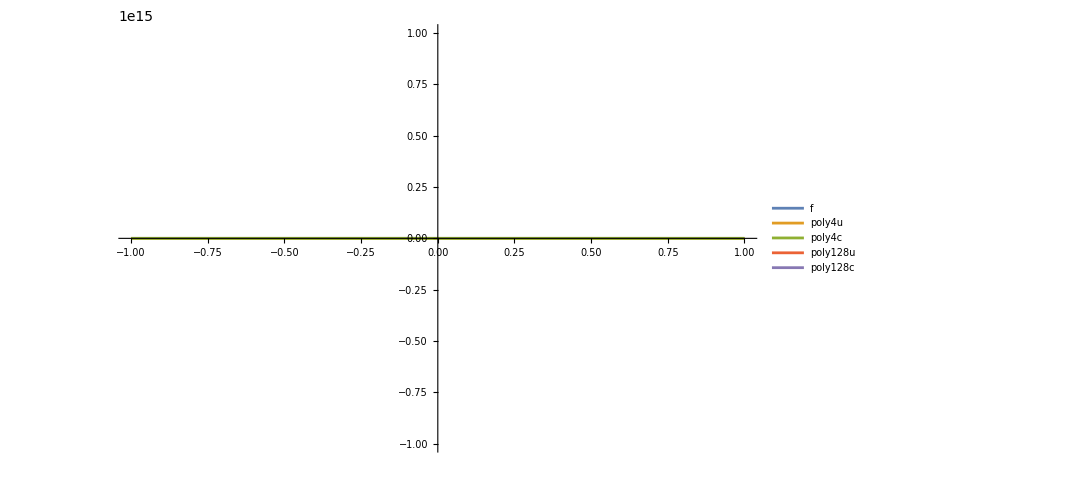

```mathematica
Plot[{f,poly4u,poly4c, poly128u,poly128c},{x,-1,1},ImageSize->800,PlotLegends->"Expressions"]
```

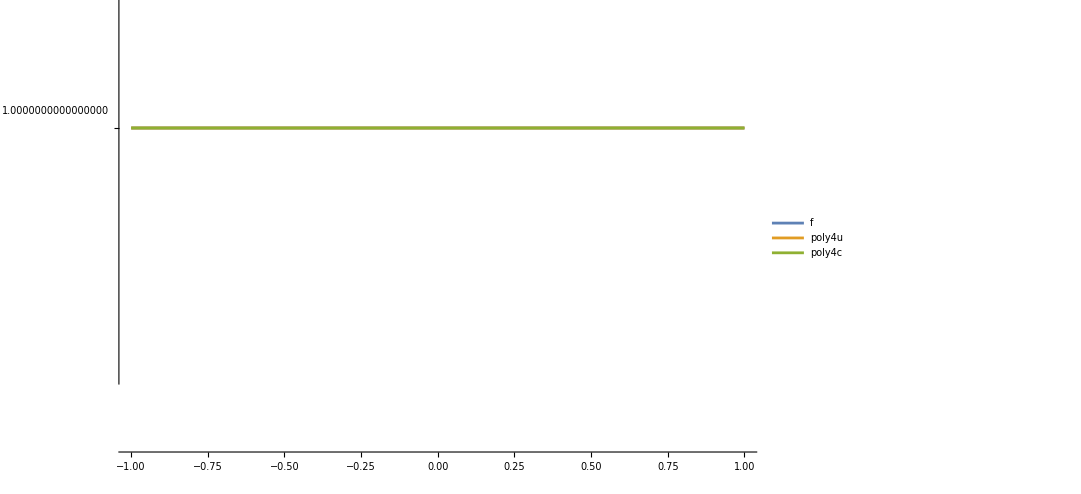

```mathematica
Plot[{f,poly4u,poly4c},{x,-1,1},ImageSize->800,PlotLegends->"Expressions"]
```